```mathematica
alldata=Import[BASEDIR<>"uchida_single_neurons/"<>"population"<>".csv"] 
data=alldata[[;;;;2]]
dataerr=alldata[[2;;;;2]]-data
```

{{0.04,2.03},{0.01,2.42},{0.33,2.61},{0.33,3.},{1.17,3.51},{1.17,3.9},{2.49,4.95},{2.49,5.46},{4.99,6.79},{4.99,7.3},{10.,9.57},{10.,10.23},{20.04,11.81},{20.04,12.63}}

{{0.04,2.03},{0.33,2.61},{1.17,3.51},{2.49,4.95},{4.99,6.79},{10.,9.57},{20.04,11.81}}

{{-0.03,0.39},{0.,0.39},{0.,0.39},{0.,0.51},{0.,0.51},{0.,0.66},{0.,0.82}}

FittedModel[1.98758+4.93952 Log[1+0.333691 u]]

{0.999392,0.692745}

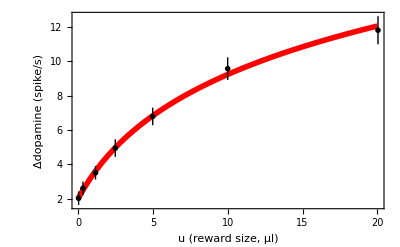

| Estimate | Standard Error | Confidence Interval
c | 1.98758 | 0.111689 | {1.67748,2.29768}
μ | 4.93952 | 0.449556 | {3.69135,6.18769}
λ | 2.99678 | 0.552188 | {1.46366,4.5299}

```mathematica
nlmLog=NonlinearModelFit[data, c+μ Log[  u/λ+1],{c,μ,λ},u,Weights->1/dataerr[[;;,2]]^2] (* μ Log[au+b]=μ Log[a/b u+1]+μ Log[b], we take c=μ Log[b] and  λ=a/b*)
Print[{nlmLog["RSquared"],nlmLog["BIC"]}]
fig=Show[Plot[nlmLog["BestFit"],{u,0,20},PlotRange->All,PlotStyle->{Red,Thickness[0.01]},Frame->True,LabelStyle->{Black,13},FrameLabel->{"u (reward size, μl)","Δdopamine (spike/s)"},PlotRange->All],
ListPlot[Evaluate[{#[[1,1]],#[[1,2]]±#[[2]]}&/@(({data,dataerr[[;;,2]]})ᵀ)],PlotStyle-> Black,PlotMarkers-> {Black,100},IntervalMarkersStyle->Directive[Thick,Black],PlotRange->All]]
Export[BASEDIR<>"figs/arithmetic.pdf",fig];

nlmLog["ParameterConfidenceIntervalTable"]
```